```mathematica
SetDirectory[NotebookDirectory[]];
fns=FileNames["780_USAF_CAL_take3-2021-03-09-155107.png"]
camdata=ImageData[Import[#],"Byte"]&/@fns;
(*camdata=Table[ImageData[ImageRotate[Image[camdata[[i]],"Byte"],π/180*13+π/2],"Byte"],{i,1,17}];*)
```

{780_USAF_CAL_take3-2021-03-09-155107.png}

```mathematica
Gaussian[A_,x_,y_,wx_,wy_]:=A Exp[-x^2/wx^2-y^2/wy^2]
```

```mathematica
data3D=Flatten[MapIndexed[{#2[[1]],#2[[2]],#1}&,camdata[[1]],{2}],1]
```

{{1,1,96},{1,2,215},{1,3,195},{1,4,184},{1,5,21},{1,6,23},{1,7,18},{1,8,18},{1,9,18},{1,10,17},{1,11,15},{1,12,20},{1,13,24},{1,14,20},{1,15,21},{1,16,23},{1,17,17},{1,18,23},{1,19,21},{1,20,18},{1,21,18},{1,22,23},{1,23,22},{1,24,21},{1,25,20},1228750,{960,1256,26},{960,1257,16},{960,1258,15},{960,1259,17},{960,1260,27},{960,1261,23},{960,1262,13},{960,1263,20},{960,1264,14},{960,1265,29},{960,1266,25},{960,1267,19},{960,1268,34},{960,1269,26},{960,1270,17},{960,1271,15},{960,1272,15},{960,1273,18},{960,1274,22},{960,1275,13},{960,1276,17},{960,1277,12},{960,1278,17},{960,1279,15},{960,1280,27}}
 |  |  |  |

```mathematica
Print[Dimensions[data3D]]
```

{1228800,3}

```mathematica
Print[Show[
Image[camdata[[1]],"Byte"],ImageSize->1000
]];
```

-Graphics-

```mathematica
nlmf = NonlinearModelFit[data3D,{A0 Exp[-2(((x-x0)/ωx0)^2+((y-(960-y0))/ωy0)^2)]+A1 Exp[-2(((x-x1)/ωx1)^2+((y-(960-y1))/ωy1)^2)]+A2 Exp[-2(((x-x2)/ωx2)^2+((y-(960-y2))/ωy2)^2)]+b},{{x0,320},{y0,362},{ωx0,10},{ωy0,10},{A0,200},{x1,320},{y1,310},{ωx1,10},{ωy1,10},{A1,200},{x2,320},{y2,260},{ωx2,10},{ωy2,10},{A2,200},{b,0}},{y,x}]
%["ParameterTable"]
```

```mathematica
FittedModel[84.60410851663231+245.5734141923697 ⅇ^(-2 («1»))+247.24781539055402 ⅇ^(«1»)+246.948361534553 ⅇ^(-2 (0.00014497802829415685 («1»)^2+«21» «1»))]
```

General::munfl: Exp[-2281.28] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1757.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1464.97] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 317.83 | 0.411774 | 771.856 | 0.
y0 | 360.054 | 0.111326 | 3234.23 | 0.
ωx0 | 83.0518 | 0.824543 | 100.725 | 0.
ωy0 | 22.3535 | 0.225591 | 99.0886 | 0.
A0 | 246.948 | 2.45449 | 100.611 | 0.
x1 | 320.038 | 0.413169 | 774.593 | 0.
y1 | 307.581 | 0.110958 | 2772.05 | 0.
ωx1 | 83.0986 | 0.827323 | 100.443 | 0.
ωy1 | 22.1617 | 0.226754 | 97.7344 | 0.
A1 | 247.248 | 2.46867 | 100.154 | 0.
x2 | 322.34 | 0.429065 | 751.262 | 0.
y2 | 255.296 | 0.107871 | 2366.68 | 0.
ωx2 | 83.6619 | 0.859112 | 97.3819 | 0.
ωy2 | 20.9722 | 0.217725 | 96.324 | 0.
A2 | 245.573 | 2.52283 | 97.3404 | 0.
b | 84.6041 | 0.0604416 | 1399.77 | 0.

```mathematica
data3D[[961]]
```

{1,961,51}

{960}

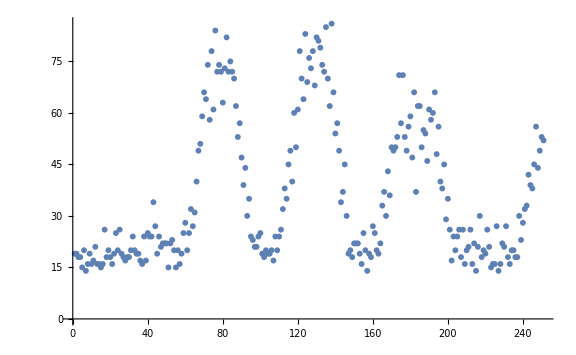

```mathematica
Test = {};
For[i=1,i≤ 960*1280,i++,If[data3D[[i]][[2]] == 734,AppendTo[Test,data3D[[i]][[3]]]]]
Print[Dimensions[Test]]
ListPlot[Test[[300;;550]],ImageSize->Large]
```

```mathematica
nlmf = NonlinearModelFit[Test[[300;;500]],{A0 Exp[-2(((x-x0)/ωx0)^2)]+A1 Exp[-2(((x-x1)/ωx1)^2)]+A2 Exp[-2(((x-x2)/ωx2)^2)]+b},{{x0,70},{ωx0,10},{A0,200},{x1,120},{ωx1,10},{A1,200},{x2,180},{ωx2,10},{A2,200},{b,0}},{x}]
%["ParameterTable"]
```

FittedModel[18.171+42.809 ⅇ^(-0.00341082 (-«18»+x)^2)+64.4798 ⅇ^(-0.00530636 («1»)^2)+60.5248 ⅇ^(-0.00609807 (-78.7705+x)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 78.7705 | 0.349462 | 225.405 | 1.06856×10^-233
ωx0 | 18.11 | 0.780008 | 23.2177 | 1.63556×10^-57
A0 | 60.5248 | 2.12085 | 28.538 | 8.33027×10^-71
x1 | 129.426 | 0.34062 | 379.972 | 6.4918×10^-277
ωx1 | 19.4141 | 0.75077 | 25.8589 | 2.65585×10^-64
A1 | 64.4798 | 2.07499 | 31.0748 | 1.26676×10^-76
x2 | 183.306 | 0.617822 | 296.697 | 1.98686×10^-256
ωx2 | 24.2151 | 1.45671 | 16.6231 | 5.79765×10^-39
A2 | 42.809 | 1.95994 | 21.842 | 7.96398×10^-54
b | 18.171 | 0.862273 | 21.0734 | 1.01289×10^-51

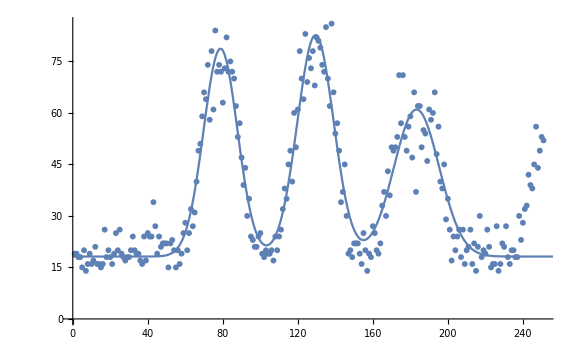

```mathematica
Show[{ListPlot[Test[[300;;550]],ImageSize->Large],Plot[{nlmf[x]},{x,0,300},PlotRange->All]}]
```

```mathematica
(*228.1 line pairs per mm for G7E6--so each line pair is 1/228.1 from center to center*)
1/228.1
((129.426-78.7705)+(183.306-129.426))/2
```

0.00438404

52.2678

```mathematica
(*so 52.2678 pixels is 4.384 µm, which is 11.92 pixels/µm*)
```

```mathematica
(*lets test with another line*)
```

{960}

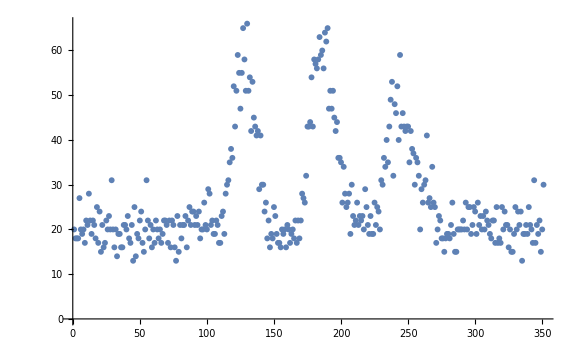

```mathematica
Test = {};
For[i=1,i≤ 960*1280,i++,If[data3D[[i]][[2]] == 592,AppendTo[Test,data3D[[i]][[3]]]]]
Print[Dimensions[Test]]
ListPlot[Test[[200;;550]],ImageSize->Large]
```

```mathematica
nlmf = NonlinearModelFit[Test[[200;;500]],{A0 Exp[-2(((x-x0)/ωx0)^2)]+A1 Exp[-2(((x-x1)/ωx1)^2)]+A2 Exp[-2(((x-x2)/ωx2)^2)]+b},{{x0,120},{ωx0,10},{A0,200},{x1,180},{ωx1,10},{A1,200},{x2,250},{ωx2,10},{A2,200},{b,0}},{x}]
%["ParameterTable"]
```

FittedModel[20.1083+26.4693 ⅇ^(-0.00440795 (-«18»+x)^2)+41.7842 ⅇ^(-0.00680971 ((«1»«1»)^2)+38.5797 ⅇ^(-0.00835117 (-127.959+x)^2)]

General::munfl: Exp[-922.614] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1040.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-954.748] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 127.959 | 0.318536 | 401.71 | 0.
ωx0 | 15.4754 | 0.664044 | 23.3047 | 1.66104×10^-68
A0 | 38.5797 | 1.39516 | 27.6524 | 2.05559×10^-83
x1 | 186.509 | 0.309507 | 602.6 | 0.
ωx1 | 17.1376 | 0.646988 | 26.4883 | 1.61478×10^-79
A1 | 41.7842 | 1.32845 | 31.4533 | 1.28003×10^-95
x2 | 244.403 | 0.544702 | 448.691 | 0.
ωx2 | 21.3008 | 1.15071 | 18.511 | 4.24977×10^-51
A2 | 26.4693 | 1.1961 | 22.1296 | 2.56051×10^-64
b | 20.1083 | 0.330502 | 60.8418 | 1.57651×10^-167

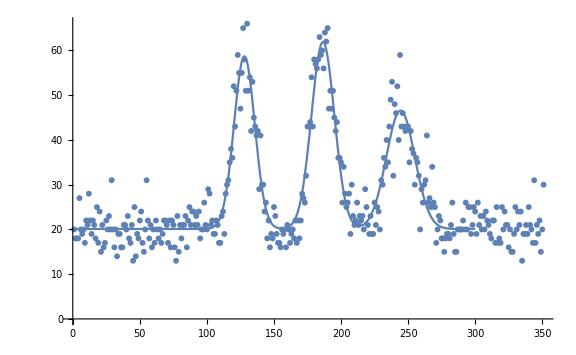

```mathematica
Show[{ListPlot[Test[[200;;550]],ImageSize->Large],Plot[{nlmf[x]},{x,0,300},PlotRange->All]}]
```

```mathematica
(*203.2 line pairs per mm for G7E5--so each line pair is 1/203.2 from center to center*)
1/203.2
((186.509-127.959)+(244.403-186.509))/2
```

0.00492126

58.222

```mathematica
(*so 58.222 pixels is 4.9212 µm, which is 11.83 pixels/µm*)
```

{960}

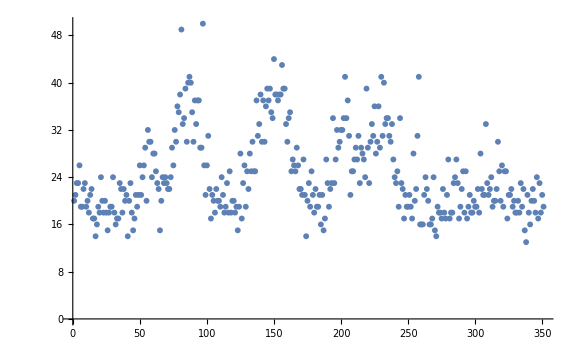

```mathematica
(*One more time for good measure*)

Test = {};
For[i=1,i≤ 960*1280,i++,If[data3D[[i]][[2]] == 385,AppendTo[Test,data3D[[i]][[3]]]]]
Print[Dimensions[Test]]
ListPlot[Test[[200;;550]],ImageSize->Large]
```

```mathematica
nlmf = NonlinearModelFit[Test[[200;;500]],{A0 Exp[-2(((x-x0)/ωx0)^2)]+A1 Exp[-2(((x-x1)/ωx1)^2)]+A2 Exp[-2(((x-x2)/ωx2)^2)]+b},{{x0,90},{ωx0,10},{A0,200},{x1,150},{ωx1,10},{A1,200},{x2,220},{ωx2,10},{A2,200},{b,0}},{x}]
%["ParameterTable"]
```

FittedModel[20.013+12.0579 ⅇ^(-0.00141899 (-«19»+x)^2)+19.5561 ⅇ^(-0.00437833 ((«1»«1»)^2)+18.5871 ⅇ^(-0.00563468 (-86.0922+x)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 86.0922 | 0.778372 | 110.606 | 8.84174×10^-240
ωx0 | 18.84 | 1.67454 | 11.2509 | 1.27056×10^-24
A0 | 18.5871 | 1.36534 | 13.6135 | 5.41283×10^-33
x1 | 149.976 | 0.793306 | 189.052 | 1.47992×10^-306
ωx1 | 21.3728 | 1.68306 | 12.6987 | 1.06837×10^-29
A1 | 19.5561 | 1.29468 | 15.105 | 1.84669×10^-38
x2 | 220.195 | 1.69955 | 129.561 | 2.25929×10^-259
ωx2 | 37.5426 | 3.82246 | 9.82159 | 7.5167×10^-20
A2 | 12.0579 | 1.00432 | 12.0061 | 3.03207×10^-27
b | 20.013 | 0.433347 | 46.1824 | 5.60936×10^-136

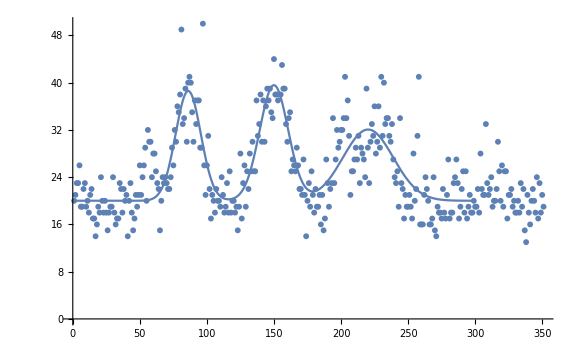

```mathematica
Show[{ListPlot[Test[[200;;550]],ImageSize->Large],Plot[{nlmf[x]},{x,0,300},PlotRange->All]}]
```

```mathematica
(*181.0 line pairs per mm for G7E4--so each line pair is 1/181.0 from center to center*)
1/181.0
((149.967-86.0922)+(220.195-149.967))/2
```

0.00552486

67.0514

```mathematica
(*so 67.0514 pixels is 5.52 µm, which is 12.15 pixels/µm*)


(*so averaged:*)
```

```mathematica
(12.15+11.83+11.92)/3
```

11.9667